```mathematica
weeks={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,24}
ghome2={6,5,3,2,5,5,8,4,8,3,2,1,6,8,6,2,2,1,1,1,1,2,3}
data=Thread[{weeks,Accumulate[ghome2]}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,24}

{6,5,3,2,5,5,8,4,8,3,2,1,6,8,6,2,2,1,1,1,1,2,3}

{{1,6},{2,11},{3,14},{4,16},{5,21},{6,26},{7,34},{8,38},{9,46},{10,49},{11,51},{12,52},{13,58},{14,66},{15,72},{16,74},{17,76},{18,77},{19,78},{20,79},{21,80},{22,82},{24,85}}

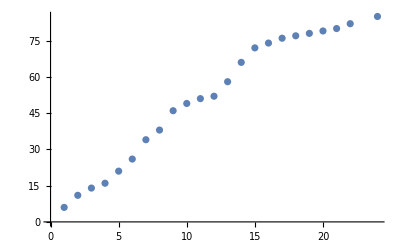

```mathematica
ListPlot[data]
```

```mathematica
goel=NonlinearModelFit[data,a*(1-Exp[-b*t]),{a,b},t]
```

FittedModel[147.581 (1-ⅇ^(-0.0390362 t))]

```mathematica
goel["BestFitParameters"]
```

{a→147.581,b→0.0390362}

```mathematica
goel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 147.581 | 17.0469 | 8.65735 | 2.26984×10^-8
b | 0.0390362 | 0.00632987 | 6.16699 | 4.05627×10^-6

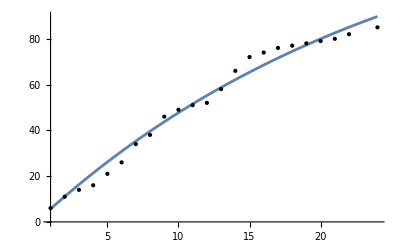

```mathematica
Plot[goel[t],{t,1,24},Epilog->Point[data]]
```

```mathematica
hdModel=NonlinearModelFit[data,Log[(Exp [a]-c)/(Exp[a*Exp[-b*t]]-c)],{{a,90},{b,0.1},c},t,Method->"Newton"];
Normal[hdModel]
```

NonlinearModelFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Log[(1.24058×10^64)/(55969.5+ⅇ^(147.581 ⅇ^(-0.0390362 t)))]

```mathematica
hdModel["BestFitParameters"]
```

{a→147.581,b→0.0390362,c→1.00016}

```mathematica
hdModel["ParameterTable"]
```

General::munfl: Exp[-1273.44] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | 147.581 | 17.4679 | 8.4487 | 4.96609×10^-8
b | 0.0390362 | 0.00648619 | 6.01836 | 6.9577×10^-6
c | -55969.5 | 3.03918×10^-24 | -1.8416×10^28 | 0.

```mathematica
Plot[hdModel[t],{t,1,24},Epilog->Point[data]]
```

-Graphics-

```mathematica
pzModel=NonlinearModelFit[data, 1/(1+β*Exp[-b*t])((c+a)(1-Exp[-b*t])-(a*b)/(b-α)(Exp[-α*t]-Exp[-b*t])),{a,b,{c,90},β,{α,1.1}},t];
Normal[pzModel]
```

(87.4769 (1-ⅇ^(-0.2127 t))-25.4794 (ⅇ^(-2.41631 t)-ⅇ^(-0.2127 t)))/(1+5.71523 ⅇ^(-0.2127 t))

```mathematica
pzModel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -263.972 | 804.882 | -0.327963 | 0.746724
b | 0.2127 | 0.0317818 | 6.69251 | 2.81659×10^-6
c | 351.448 | 805.527 | 0.436296 | 0.66781
β | 5.71523 | 2.55386 | 2.23788 | 0.0381111
α | 2.41631 | 8.28534 | 0.291637 | 0.773898

```mathematica
pzModel["BestFitParameters"]
```

{a→-263.972,b→0.2127,c→351.448,β→5.71523,α→2.41631}

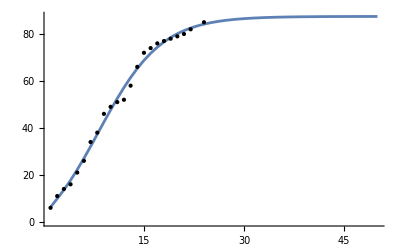

```mathematica
Plot[pzModel[t],{t,1,50},Epilog->Point[data]]
```

```mathematica
pnzModel=NonlinearModelFit[data,a/(1+β*Exp[-b*t])((1-Exp[-b*t])(1-α/b)+α*t),{{a,90},{b,0.1},α,β},t,MaxIterations->Infinity,PrecisionGoal->Infinity];
Normal[pnzModel]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

(134.991 (1.11097 (1-ⅇ^(-0.139956 t))-0.0155313 t))/(1+3.76977 ⅇ^(-0.139956 t))

```mathematica
pnzModel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 134.991 | 75.8084 | 1.78068 | 0.0909606
b | 0.139956 | 0.0497753 | 2.81175 | 0.0111348
α | -0.0155313 | 0.0169609 | -0.915712 | 0.371294
β | 3.76977 | 0.973461 | 3.87255 | 0.00102511

```mathematica
pnzModel["BestFitParameters"]
```

{a→134.991,b→0.139956,α→-0.0155313,β→3.76977}

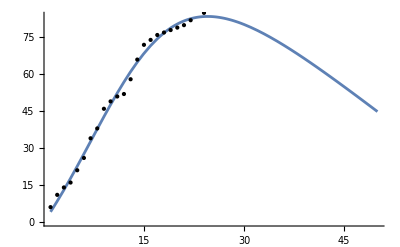

```mathematica
Plot[pnzModel[t],{t,1,50},Epilog->Point[data]]
```

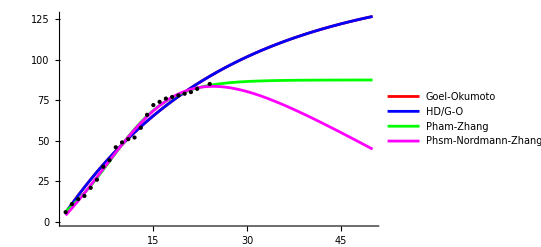

```mathematica
Plot[{goel[x],hdModel[x],pzModel[x],pnzModel[x]},{x,1,50},PlotStyle-> {Red,Blue,Green,Magenta},PlotLegends->{"Goel-Okumoto","HD/G-O ","Pham-Zhang","Phsm-Nordmann-Zhang"},Epilog->Point[data]]
```

```mathematica
A1={#,goel[#],hdModel[#],pzModel[#],pnzModel[#]}&[{"AIC","BIC"}]Flatten[#]& /@MapThread[List,{{"model","Goel-Okumoto","HD/G-O ","Pham-Zhang","Phsm-Nordmann-Zhang"},A1}];
Grid[%,Frame->All]
```

Thread::tdlen: Objects of unequal length in {{AIC,BIC},{127.126,130.532},{129.248,133.79},{109.194,116.007},{109.045,114.722}} {model,«6»,AdjustedRSquared FittedModel[134.991 («2»)^2][{«1»}]} cannot be combined.

Thread::tdlen: Objects of unequal length in {{AIC,BIC},{127.126,130.532},{129.248,133.79},{109.194,116.007},{109.045,114.722}} {Goel-Okumoto,«6»,0.9963 «11»[134.991 («2»)^2][{«1»}]} cannot be combined.

Thread::tdlen: Objects of unequal length in {{AIC,BIC},{127.126,130.532},{129.248,133.79},{109.194,116.007},{109.045,114.722}} {HD/G-O ,«6»,0.996115 FittedModel[134.991 («2»)^2][{«1»}]} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Grid[{{{AIC,BIC},{127.126,130.532},{129.248,133.79},{109.194,116.007},{109.045,114.722}} {model,AIC model,BIC model,model Null,AIC FittedModel[147.581 (1-ⅇ^(-0.0390362 t))][{AIC,BIC,Null}],BIC FittedModel[Log[(1.24058×10^64)/(55969.5+ⅇ^(«19» «1»))]][{AIC,BIC,Null}],RSquared FittedModel[(87.4769 (1-ⅇ^(«1»))-«18» («1»-«1»))/(1+5.71523 ⅇ^(-«20»«1»«1»))][{AIC,BIC,Null}],AdjustedRSquared FittedModel[(134.991 («19» (1-ⅇ^(«1»))-«1»))/(1+3.76977 ⅇ^(-«20»«1»«1»))][{AIC,BIC,Null}]},{{AIC,BIC},{127.126,130.532},{129.248,133.79},{109.194,116.007},{109.045,114.722}} {Goel-Okumoto,AIC Goel-Okumoto,BIC Goel-Okumoto,Goel-Okumoto Null,127.126 FittedModel[147.581 (1-ⅇ^(-0.0390362 t))][{AIC,BIC,Null}],130.532 FittedModel[Log[(1.24058×10^64)/(55969.5+ⅇ^(«19» «1»))]][{AIC,BIC,Null}],0.996622 FittedModel[(87.4769 (1-ⅇ^(«1»))-«18» («1»-«1»))/(1+5.71523 ⅇ^(-«20»«1»«1»))][{AIC,BIC,Null}],0.9963 FittedModel[(134.991 («19» (1-ⅇ^(«1»))-«1»))/(1+3.76977 ⅇ^(-«20»«1»«1»))][{AIC,BIC,Null}]},{{AIC,BIC},{127.126,130.532},{129.248,133.79},{109.194,116.007},{109.045,114.722}} {HD/G-O ,AIC HD/G-O ,BIC HD/G-O ,HD/G-O  Null,129.248 FittedModel[147.581 (1-ⅇ^(-0.0390362 t))][{AIC,BIC,Null}],133.79 FittedModel[Log[(1.24058×10^64)/(55969.5+ⅇ^(«19» «1»))]][{AIC,BIC,Null}],0.996622 FittedModel[(87.4769 (1-ⅇ^(«1»))-«18» («1»-«1»))/(1+5.71523 ⅇ^(-«20»«1»«1»))][{AIC,BIC,Null}],0.996115 FittedModel[(134.991 («19» (1-ⅇ^(«1»))-«1»))/(1+3.76977 ⅇ^(-«20»«1»«1»))][{AIC,BIC,Null}]},{{AIC,BIC},{127.126,130.532},{129.248,133.79},{109.194,116.007},{109.045,114.722}} {Pham-Zhang,AIC Pham-Zhang,BIC Pham-Zhang,Pham-Zhang Null,109.194 FittedModel[147.581 (1-ⅇ^(-0.0390362 t))][{AIC,BIC,Null}],116.007 FittedModel[Log[(1.24058×10^64)/(55969.5+ⅇ^(«19» «1»))]][{AIC,BIC,Null}],0.998835 FittedModel[(87.4769 (1-ⅇ^(«1»))-«18» («1»-«1»))/(1+5.71523 ⅇ^(-«20»«1»«1»))][{AIC,BIC,Null}],0.998511 FittedModel[(134.991 («19» (1-ⅇ^(«1»))-«1»))/(1+3.76977 ⅇ^(-«20»«1»«1»))][{AIC,BIC,Null}]},{Phsm-Nordmann-Zhang,{Phsm-Nordmann-Zhang,FittedModel[(134.991 («19» (1-ⅇ^(«1»))-«1»))/(1+3.76977 ⅇ^(-«20»«1»«1»))]} {{AIC,BIC,Null},FittedModel[147.581 (1-ⅇ^(-0.0390362 t))][{AIC,BIC,Null}],FittedModel[Log[(1.24058×10^64)/(55969.5+ⅇ^(«19» «1»))]][{AIC,BIC,Null}],FittedModel[(87.4769 (1-ⅇ^(«1»))-«18» («1»-«1»))/(1+5.71523 ⅇ^(-«20»«1»«1»))][{AIC,BIC,Null}],FittedModel[(134.991 («19» (1-ⅇ^(«1»))-«1»))/(1+3.76977 ⅇ^(-«20»«1»«1»))][{AIC,BIC,Null}]}} {{AIC,BIC},{127.126,130.532},{129.248,133.79},{109.194,116.007},{109.045,114.722}}},Frame→All]

```mathematica
prediction = Table[{i,Round[pzModel[i]]},{i,25,50}]
```

{{25,85},{26,85},{27,86},{28,86},{29,86},{30,87},{31,87},{32,87},{33,87},{34,87},{35,87},{36,87},{37,87},{38,87},{39,87},{40,87},{41,87},{42,87},{43,87},{44,87},{45,87},{46,87},{47,87},{48,87},{49,87},{50,87}}

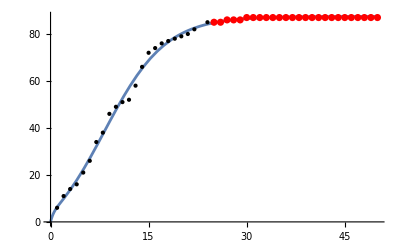

Plot::nonopt: Options expected (instead of Epilog-Point[data]) beyond position 2 in Plot[pzModel[x],{x,0,50},Epilog-Point[data]]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[Plot[pzModel[x],{x,0,50},Epilog-Point[data]],].

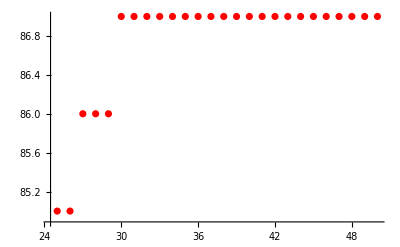
Show[Plot[pzModel[x],{x,0,50},Epilog-Point[data]],-Graphics-]

```mathematica
Show[Plot[pzModel[x],{x,0,50},Epilog->Point[data]],ListPlot[prediction,PlotStyle->Red]]
```